```mathematica
(*This code generates the numbers for the third calculation in Section V of the revision of "Bounded extremum seeking for static quadratic maps using nonlinear transformation and Lyapunov method".*)


(* This shows how to satisfy (2) *)
H={{2,0},{0,2}};
P=RiccatiSolve[{-0.5*H,{{0,0},{0,0}}},{{{1,0},{0,1}},{{1,0},{0,1}}}];
q0=1 / Max[Eigenvalues[P]];
-0.5*P.H-0.5*Transpose[H].P+q0*P
```

{{0.,0.},{0.,0.}}

```mathematica
p1=Norm[P];(* \bar p*)
p2=Min[Eigenvalues[P]];(* \underline p*)
k=11.1;
s0=Sqrt[2];(* \sigma_0*)
a1=.00022;(* \alpha*)
d1=0;(* \bar\delta*)
h1=Norm[k*a1*H];(* \bar h*)
q=k*a1*q0;
e1=0.65; (* \epsilon*)
L1=2;(*l, where \omega_2=l\omega_1*)
M1=(1/(2Pi))*(0.25+L1*Sqrt[L1] /(L1^2-1));(* \bar M*) 
N1=(1/(Pi))*(0.25+Sqrt[L1] /(2(L1+1)));(* \bar N*)  
v1=Sqrt[2] (1+Sqrt[L1])*h1*Sqrt[(L1+1)/L1]*p1*(1+2 M1*e1*h1)*Sqrt[e1/Pi]+2 p1*(1+2 M1*e1*h1)*Sqrt[1+L1]*Sqrt[2 Pi/e1]*k*(1+h1*(1+(1/L1))*e1/(2 Pi)) d1;(*\nu_1*)
v2=2*p1*N1*h1^2*e1*Sqrt[1+L1]*Sqrt[1+(1/L1)]+4 p1*M1*h1^2*(1+Sqrt[L1])*e1+2 p1*k*h1*d1*(1+2 M1*e1*h1)*Sqrt[1+L1]*Sqrt[1+(1/L1)];(*\nu_2*)
v3=2 p1*N1*h1^2*Sqrt[2 Pi*e1*(L1+1)];(*\nu_3*)
c1=27*v3 /(32*Sqrt[2]*p2*Sqrt[p2]);(*c *)
L2=(1/(2c1))*(q/3-Sqrt[(q /3)^2-3 *c1*v1 /(Sqrt[2*p2])]);(* \lambda_s*)
L3= (1/(2c1))*(q/3+Sqrt[(q /3)^2-3 *c1*v1 /(Sqrt[2*p2])]);(* \lambda_l*)
W1=(9*p1/8)*(s0/Sqrt[a1]+Sqrt[(1+(1/L1))*(e1/(2 Pi))])^2; (*square of left side of (15) *)
```

```mathematica
(*The following should be positive to apply the method.*)
0.25*p2*q-v2
(p2/(18*p1*M1*h1))-e1
(q/3)^2-(3*c1*v1/(Sqrt[2]*p2))
L3^2-W1
```

0.000591203

59.2685

2.2206×10^-6

104.444

```mathematica
(* This gives the ultimate bound *)
1.5*L2*Sqrt[a1/(2p2)]+Sqrt[(e1*a1/(2Pi))*(1+(1/Sqrt[L1]))]
```

0.0553486

```mathematica
D1[t_]=0; (* \delta(t) *)
```

```mathematica
newrror1=NDSolve[{x1'[t]==Sqrt[a1*2Pi/e1]*Cos[(2Pi/e1)*t+k*((x1[t])^2+(x2[t])^2)+k*D1[t]],
x2'[t]==Sqrt[a1*L1*2Pi/e1]*Cos[(2Pi*L1/e1)*t+k*((x1[t])^2+(x2[t])^2)+k*D1[t]],
x1[t/;t≤0]==1,x2[t/;t≤0]==-1},{x1,x2},{t,0,3200},MaxSteps->1000000,  AccuracyGoal->3,PrecisionGoal->3];
```

```mathematica
P1=Plot[x1[t]/.newrror1,{t,0,3200}, AxesLabel->{ t [sec],OverTilde["θ"] },     AxesStyle->Thick,PlotStyle->{Dashed, Thickness[0.0049],RGBColor[1,0,0]},PlotRange->{{0,3200},{-1.1,1.1}}, LabelStyle->{FontFamily->"Times",FontSize ->20,FontWeight->"Bold",FontColor->Black},ImageSize->Large];

P2=Plot[x2[t]/.newrror1,{t,0, 3200},    AxesLabel->{ t [sec],OverTilde["θ"] }, AxesStyle->Thick,PlotStyle->{ Thickness[0.0049],RGBColor[0,0,1]},PlotRange->{{0,3200},{-1.1,1.1}}, LabelStyle->{FontFamily->"Times",FontSize ->20,FontWeight->"Bold",FontColor->Black},ImageSize->Large];
```

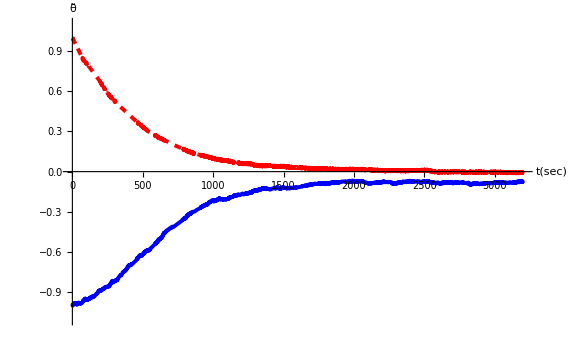

```mathematica
Show[P1,P2]
```